```mathematica
<<"MaTeX`"
tex[x_,fontsize_]:=MaTeX[x,FontSize->fontsize];

tf[n1_,n2_,x1_,x2_,k1_,k2_,f_,b_,s_,w_,if_]:=MapThread[Prepend,{Flatten[Riffle[{{#,{-if,-1}1/(5w)}}&/@MaTeX[NumberForm[#,{f,b}]&/@#[1,{x1,x2}],FontSize->s],{Table[{Null,{-if,-1}1/(8w)},k2-1]},2],1],#[k2,{n1,n2}]}]&[Rescale[Subdivide[n1,n2,#1 k1],{n1,n2},#2]&];
tf[n1_,n2_,k1_,k2_,s_,w_,if_]:=tf[n1,n2,n1,n2,k1,k2,1,1,s,w,if];
tf[n1_,n2_,k1_,k2_,s_,w_]:=tf[n1,n2,n1,n2,k1,k2,1,1,s,w,0];
```

### Exact Hubbard model solution for Li_2 molecule using (2s)^2 orbital basis.

```mathematica
H =({{2e, 0, V, V, 0, 0}, {0, 2e, V, V, 0, 0}, {V, V, 2e+U, 0, 0, 0}, {V, V, 0, 2e+U, 0, 0}, {0, 0, 0, 0, 2e, 0}, {0, 0, 0, 0, 0, 2e}});
```

```mathematica
ϕ1 = {1,0,0,0,0,0};
ϕ2 = {0,1,0,0,0,0};
ϕ3 = {0,0,1,0,0,0};
ϕ4 = {0,0,0,1,0,0};
ϕ5 = {0,0,0,0,1,0};
ϕ6 = {0,0,0,0,0,1};

ϕa = (ϕ1+ϕ2)/√2;
ϕb = (ϕ3+ϕ4)/√2;

ϕc = (ϕ1-ϕ2)/√2;
ϕd = (ϕ3-ϕ4)/√2;

ψ[η_] :=1/(√2)(2Sin[η]Cos[η]ϕb + ϕa )//Simplify
```

```mathematica
hs = {{ϕa.H.ϕa,ϕa.H.ϕb},{ϕb.H.ϕa,ϕb.H.ϕb}};
Eigenvalues[hs]
```

{1/2 (4 e+U-√(U^2+16 V^2)),1/2 (4 e+U+√(U^2+16 V^2))}

```mathematica
Eigenvectors[hs]
```

{{-(U+√(U^2+16 V^2))/(4 V),1},{-(U-√(U^2+16 V^2))/(4 V),1}}

```mathematica
ha = {{ϕc.H.ϕc,ϕc.H.ϕd},{ϕd.H.ϕc,ϕd.H.ϕd}};
Eigenvalues[hs]
```

{1/2 (4 e+U-√(U^2+16 V^2)),1/2 (4 e+U+√(U^2+16 V^2))}

```mathematica
Eigenvalues[ha]
```

{2 e,2 e+U}

```mathematica
huhf = ψ[η].H.ψ[η]//Simplify
huhf /.{e-> 0,V-> -1}/.η-> π/4
```

e+4 V Cos[η] Sin[η]+2 (2 e+U) Cos[η]^2 Sin[η]^2

-2+U/2

```mathematica
{1/2 (4 e+U-√(U^2+16 V^2)),1/2 (4 e+U+√(U^2+16 V^2))}//TeXForm
```

\left\{\frac{1}{2} \left(4 e-\sqrt{U^2+16 V^2}+U\right),\frac{1}{2} \left(4
   e+\sqrt{U^2+16 V^2}+U\right)\right\}

```mathematica
huhf = 2 (e+(2 e+U) Cos[η]^2 Sin[η]^2+V Sin[2 η])
```

2 (e+(2 e+U) Cos[η]^2 Sin[η]^2+V Sin[2 η])

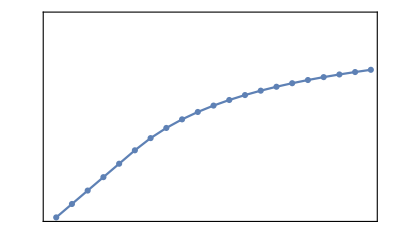

```mathematica
uhf = ListPlot[Table[{U,FindMinimum[huhf /.{e-> 0.0,V-> -1.0},{η,0.2π},AccuracyGoal->4,PrecisionGoal->4][[1]]},{U,1,5,0.2}],
Joined->{True,True},PlotMarkers-> {Automatic},
PlotLegends->{tex["E_\\text{UHF}",20]},
FrameLabel-> {tex["U/t",20],tex["E_\\text{UHF}",20]},
FrameTicks->{{tf[-2.0,0.5,4,5,10.5*100/72,10],None},{tf[0,5,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]
]
```

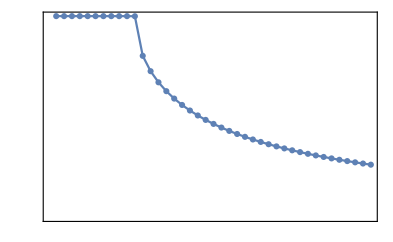

```mathematica
mix = ListPlot[Table[{U,η/.FindMinimum[huhf /.{e-> 0,V-> -1},{η,0.2π},AccuracyGoal->4,PrecisionGoal->4][[2]]},{U,1,5,0.1}],
Joined->{True,True},PlotMarkers-> {Automatic},
FrameLabel-> {tex["U/t",20],tex["\\eta_\\text{opt}",20]},
FrameTicks->{{tf[0,π/4,4,5,10.5*100/72,10],None},{tf[1,5,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

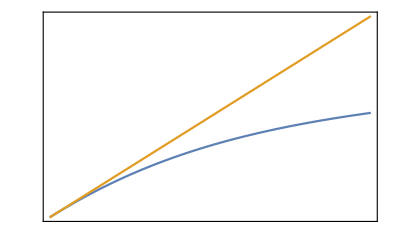

```mathematica
em = 2e + U/2 - √((U/2)^2+4 V^2)/.{e-> 0,V-> -1};
rhf = U/2 - 2;
p2 = Plot[{em,rhf},{U,0,5},PlotLegends->{tex["E_\\text{exact}",20],tex["E_\\text{RHF}",20]},
FrameLabel-> {tex["U/t",20],tex["E_\\text{UHF}",20]},
FrameTicks->{{tf[-2,0.5,4,5,10.5*100/72,10],None},{tf[0,5,4,5,10.5*100/72,10],None}},
Frame->True,
ImageSize->10*100/2.54,
FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

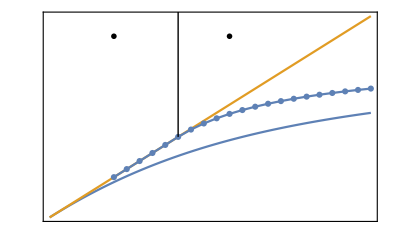

```mathematica
var = Show[p2,uhf,
Epilog-> {Line[{{2,1},{2,-1}}],
Style[Text[tex["\\text{Delocalized}",14],{1.0,0.25}],14],
Style[Text[tex["\\text{Localized}",14],{2.8,0.25}],14]
}]
```